```mathematica
ClearAll[RotMatrix];
ClearAll[gxxlab,gxylab,gxzlab,gyxlab,gyylab,gyzlab,gzxlab,gzylab,gzzlab,Gzz,Gxx,Gxz,geff,g1];

beta=14*10^-1;(*14*10^5 Hz/G*)
h=1;(*1.05*10^-34 J*s*)
w=9.75*10^3 ;(*Hz; MW frequency*)

gzTrue=2.38;
gyTrue=2.25;
gxTrue=2.25;

d=-23.89;
e=3.14;
λ=e/d;

gzz=gzTrue*(1+2/Sqrt[1+3λ^2]);
gyy=gyTrue*(1-(1+3*λ)/Sqrt[1+3λ^2]);
gxx=gxTrue*(1-(1-3*λ)/Sqrt[1+3λ^2]);


gPAS={{gxx,0,0},{0,gyy,0},{0,0,gzz}};
sig={{151.5,-8.7,1.5},{-6.9,131.0,-5.0},{5.1,-2.8,119.4}};
(*gPAS={{1,0,0},{0,2,0},{0,0,3}};*)

RotMatrix [α_,β_,γ_]:={
{Cos[α]Cos[β]Cos[γ]-Sin[α]Sin[γ],-Cos[α]Cos[β]Sin[γ]-Sin[α]Cos[γ],Cos[α]Sin[β]},
{Sin[α]Cos[β]Cos[γ]+Cos[α]Sin[γ],-Sin[α]Cos[β]Sin[γ]+Cos[α]Cos[γ],Sin[α]Sin[β]},
{-Sin[β]Cos[γ],Sin[β]Sin[γ],Cos[β]}
};

gLAB[α_,β_,γ_]:=RotMatrix[α,β,γ].gPAS.Transpose[RotMatrix[α,β,γ]];
gLAB2[α_,β_,γ_]:=RotMatrix[α,β,γ].sig.Transpose[RotMatrix[α,β,γ]];
(*RotMatrix[Pi/2,0,0]//MatrixForm*)

a={{"xx","xy","xz"},{"yx","yy","yz"},{"zx","zy","zz"}};
Transpose[a].a//MatrixForm

gxxlab[α_,β_,γ_]:=gLAB[α,β,γ][[1,1]];
gxylab[α_,β_,γ_]:=gLAB[α,β,γ][[1,2]];
gxzlab[α_,β_,γ_]:=gLAB[α,β,γ][[1,3]];
gyxlab[α_,β_,γ_]:=gLAB[α,β,γ][[2,1]];
gyylab[α_,β_,γ_]:=gLAB[α,β,γ][[2,2]];
gyzlab[α_,β_,γ_]:=gLAB[α,β,γ][[2,3]];
gzxlab[α_,β_,γ_]:=gLAB[α,β,γ][[3,1]];
gzylab[α_,β_,γ_]:=gLAB[α,β,γ][[3,2]];
gzzlab[α_,β_,γ_]:=gLAB[α,β,γ][[3,3]];

(*Original; aTranspose[a]*)
(*Gzz[α_,β_,γ_]:=gzxlab[α,β,γ]^2 + gzylab[α,β,γ]^2 + gzzlab[α,β,γ]^2;
Gxx[α_,β_,γ_]:=gxxlab[α,β,γ]^2+gxylab[α,β,γ]^2+gxzlab[α,β,γ]^2;
Gxz[α_,β_,γ_]:=(gxxlab[α,β,γ]*gzxlab[α,β,γ]+gxylab[α,β,γ]*gzylab[α,β,γ]+gxzlab[α,β,γ]*gzzlab[α,β,γ]);*)

Gzz[α_,β_,γ_]:=gxzlab[α,β,γ]^2 + gyzlab[α,β,γ]^2 + gzzlab[α,β,γ]^2;
Gxx[α_,β_,γ_]:=gxxlab[α,β,γ]^2+gyxlab[α,β,γ]^2+gzxlab[α,β,γ]^2;
Gxz[α_,β_,γ_]:=(gxxlab[α,β,γ]*gxzlab[α,β,γ]+gyxlab[α,β,γ]*gyzlab[α,β,γ]+gzxlab[α,β,γ]*gzzlab[α,β,γ]);

geff[α_,β_,γ_]:=Sqrt[Gzz[α,β,γ]];
g1[α_,β_,γ_]:=Sqrt[Gxx[α,β,γ]-((Gxz[α,β,γ])^2)/(Gzz[α,β,γ])];

gLAB[Pi/3,Pi/3,Pi/3]//MatrixForm
gLAB2[Pi/4,Pi/6,Pi/3]//MatrixForm
```

(xx^2+yx^2+zx^2 | xx xy+yx yy+zx zy | xx xz+yx yz+zx zz
xx xy+yx yy+zx zy | xy^2+yy^2+zy^2 | xy xz+yy yz+zy zz
xx xz+yx yz+zx zz | xy xz+yy yz+zy zz | xz^2+yz^2+zz^2)

(1.38912 | 2.68339 | 0.852475
2.68339 | 3.62258 | 2.77412
0.852475 | 2.77412 | 2.12181)

(128.973 | 1.14697 | 0.196352
0.596969 | 152.011 | -10.9454
-3.09727 | -7.80068 | 120.916)

{x→1.48766}

762

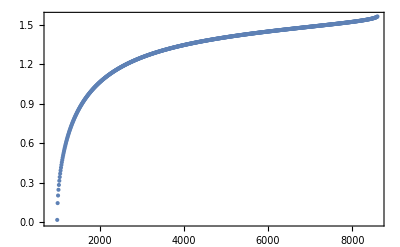

```mathematica
FindRoot[h w/beta/(geff[0,x,0])==7000,{x,1}]

data=Table[i,{i,992,8609,10}];

test=x/.Map[FindRoot[h w/beta/geff [0.0,x,0.]== #, {x,1.5}]&, data];

(*a=FindRoot[h w/beta/geff [x]== 992, {x,1}];*)
Length[test]
finaldata=Table[{i//N,h w/beta/geff[0.,i,0.]},{i,test}];
ListPlot[Transpose@{finaldata[[All,2]],finaldata[[All,1]]},PlotRange->All, Frame->True]

(*Export["points635.csv",finaldata,"CSV"]*)

(*Length@finaldata*)
```

```mathematica
step = Pi/6;

(*ParallelTable[{
h w/beta/geff[0,i,0],Parallelize@Apply[Plus,Flatten[ParallelTable[(g1[x,i,y])^2,{x,0,Pi,step*5},{y,0,Pi,step*5}]]]
},
{i,0,Pi/2,step}];*)

data2=
ParallelTable[{
h w/beta/geff[x,i,y],(N@g1[x,i,y])^2
},{x,0,Pi,step},{i,0,Pi/2,step},{y,0,Pi,step}
];
```

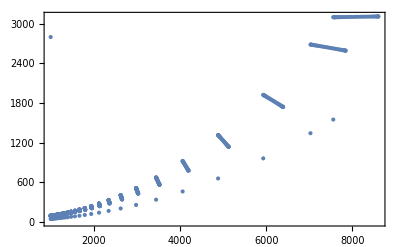

```mathematica
(*Split[data3,Last[#2]≥Last[#1]&]
Length[Flatten[%]]*)
data3=Partition[Flatten[data2],2];
data4=Sort[data3,#1[[1]]<#2[[1]]&];
data5=Split[data4,Round[#1[[1]],0.0000001]≥(Round[#2[[1]],0.0000001])&];
(*DeleteDuplicates[data4[[All,1]]];*)
data6=Transpose[{DeleteDuplicates[Round[data4[[All,1]],0.0000001]],Map[Apply[Plus,#]&,data5[[All,All,2]]]}];
ListPlot[data6,Frame->True,PlotRange->All]
```

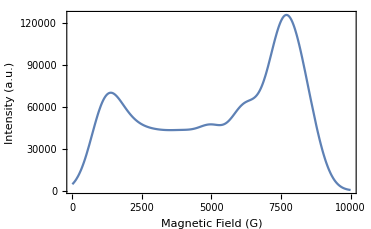

```mathematica
(*Convolutioin with Gauss*)
ClearAll[f];
Off[General::munfl];
Gauss[x0_,x_,width_,ampl_]:=Exp[-(x-x0)(x-x0)/(2width width)];
f[x_]:=Apply[Plus,MapThread[Times,{Map[Gauss[#,x,500,10]&,data6[[All,1]]],data6[[All,2]]}]];
(*g[x_]:=Apply[Plus,MapThread[Times,{Map[Gauss[#,x,0.030,10]&,data2[[All,1]]],data2[[All,2]]/1.02}]]*)
gr1=Plot[{f[x](*,g[x]*)},{x,0,10000},PlotRange->All,Frame->True,FrameLabel->{"Magnetic Field (G)", "Intensity (a.u.)"}]
```

```mathematica
data2
```

{{{{991.887,0.654362},{991.887,0.702919},{991.887,0.800034},{991.887,0.848591},{991.887,0.800034},{991.887,0.702919},{991.887,0.654362}},{{1142.81,0.868639},{1142.62,0.932792},{1142.25,1.06097},{1142.06,1.125},{1142.25,1.06097},{1142.62,0.932792},{1142.81,0.868639}},{{1945.42,2.51721},{1942.66,2.69634},{1937.18,3.05157},{1934.45,3.22768},{1937.18,3.05157},{1942.66,2.69634},{1945.42,2.51721}},{{8609.29,49.298},{8306.61,49.298},{7786.14,49.298},{7560.1,49.298},{7786.14,49.298},{8306.61,49.298},{8609.29,49.298}}},{{{991.887,0.702919},{991.887,0.800034},{991.887,0.848591},{991.887,0.800034},{991.887,0.702919},{991.887,0.654362},{991.887,0.702919}},{{1142.81,0.863627},{1142.62,0.983296},{1142.25,1.0551},{1142.06,1.00734},{1142.25,0.887796},{1142.62,0.815885},{1142.81,0.863627}},{{1945.42,2.10006},{1942.66,2.36186},{1937.18,2.60321},{1934.45,2.58435},{1937.18,2.32539},{1942.66,2.08246},{1945.42,2.10006}},{{8609.29,37.1856},{8306.61,37.171},{7786.14,37.147},{7560.1,37.1371},{7786.14,37.147},{8306.61,37.171},{8609.29,37.1856}}},{{{991.887,0.800034},{991.887,0.848591},{991.887,0.800034},{991.887,0.702919},{991.887,0.654362},{991.887,0.702919},{991.887,0.800034}},{{1142.81,0.853603},{1142.62,0.916893},{1142.25,0.876048},{1142.06,0.772021},{1142.25,0.708746},{1142.62,0.749482},{1142.81,0.853603}},{{1945.42,1.26575},{1942.66,1.4135},{1937.18,1.42868},{1934.45,1.29769},{1937.18,1.15086},{1942.66,1.1341},{1945.42,1.26575}},{{8609.29,12.9609},{8306.61,12.917},{7786.14,12.845},{7560.1,12.8153},{7786.14,12.845},{8306.61,12.917},{8609.29,12.9609}}},{{{991.887,0.848591},{991.887,0.800034},{991.887,0.702919},{991.887,0.654362},{991.887,0.702919},{991.887,0.800034},{991.887,0.848591}},{{1142.81,0.848591},{1142.62,0.799986},{1142.25,0.702872},{1142.06,0.654362},{1142.25,0.702872},{1142.62,0.799986},{1142.81,0.848591}},{{1945.42,0.848591},{1942.66,0.799621},{1937.18,0.702509},{1934.45,0.654362},{1937.18,0.702509},{1942.66,0.799621},{1945.42,0.848591}},{{8609.29,0.848591},{8306.61,0.789971},{7786.14,0.694078},{7560.1,0.654362},{7786.14,0.694078},{8306.61,0.789971},{8609.29,0.848591}}},{{{991.887,0.800034},{991.887,0.702919},{991.887,0.654362},{991.887,0.702919},{991.887,0.800034},{991.887,0.848591},{991.887,0.800034}},{{1142.81,0.853603},{1142.62,0.749482},{1142.25,0.708746},{1142.06,0.772021},{1142.25,0.876048},{1142.62,0.916893},{1142.81,0.853603}},{{1945.42,1.26575},{1942.66,1.1341},{1937.18,1.15086},{1934.45,1.29769},{1937.18,1.42868},{1942.66,1.4135},{1945.42,1.26575}},{{8609.29,12.9609},{8306.61,12.917},{7786.14,12.845},{7560.1,12.8153},{7786.14,12.845},{8306.61,12.917},{8609.29,12.9609}}},{{{991.887,0.702919},{991.887,0.654362},{991.887,0.702919},{991.887,0.800034},{991.887,0.848591},{991.887,0.800034},{991.887,0.702919}},{{1142.81,0.863627},{1142.62,0.815885},{1142.25,0.887796},{1142.06,1.00734},{1142.25,1.0551},{1142.62,0.983296},{1142.81,0.863627}},{{1945.42,2.10006},{1942.66,2.08246},{1937.18,2.32539},{1934.45,2.58435},{1937.18,2.60321},{1942.66,2.36186},{1945.42,2.10006}},{{8609.29,37.1856},{8306.61,37.171},{7786.14,37.147},{7560.1,37.1371},{7786.14,37.147},{8306.61,37.171},{8609.29,37.1856}}},{{{991.887,0.654362},{991.887,0.702919},{991.887,0.800034},{991.887,0.848591},{991.887,0.800034},{991.887,0.702919},{991.887,0.654362}},{{1142.81,0.868639},{1142.62,0.932792},{1142.25,1.06097},{1142.06,1.125},{1142.25,1.06097},{1142.62,0.932792},{1142.81,0.868639}},{{1945.42,2.51721},{1942.66,2.69634},{1937.18,3.05157},{1934.45,3.22768},{1937.18,3.05157},{1942.66,2.69634},{1945.42,2.51721}},{{8609.29,49.298},{8306.61,49.298},{7786.14,49.298},{7560.1,49.298},{7786.14,49.298},{8306.61,49.298},{8609.29,49.298}}}}